## Demo for the options

```mathematica
M2TeXToString[tasfasdfsdafest]
M2TeXToString[3242434]
M2TeXToString[{asdfasdf}]
```

```mathematica
test=M2TeXSetCommand["usepackage"];
M2TeXToString[test]
```

```mathematica
test=M2TeXSetCommand[
"usepackage",
"Parameter"->{1,2,3,4},
"OptionalParameter"->{1,2,3}
];
M2TeXToString[test]
```

```mathematica
test=M2TeXSetPackage[
"Parameter"->{1,2,3,4}
];
M2TeXToString[test]
```

```mathematica
M2TeXSetOptionalOption[{1,2,3,4}];
M2TeXToString[%]
```

```mathematica
test=M2TeXSetPackage[
"ParameterList"->{
M2TeXSetOption[asfasf],
M2TeXSetOptionalOption[{1,2,3,4}]
}
];
M2TeXToString[test]
```

```mathematica
test=M2TeXSetEnvironment[
"document",
"ParameterList"->{
M2TeXSetOption[asfasf],
M2TeXSetOptionalOption[{1,2,3,4}]
}
];
M2TeXToString[test]
```

```mathematica
AppendTo
```

```mathematica
abc=f[{1,2,3}]
```

```mathematica
AppendTo[abc⟦1⟧,5]
```

```mathematica
abc
```

```mathematica
M2TeXSetDocument[]
M2TeXToString[%]
```

```mathematica
M2TeXDocumentToString[]
```

```mathematica
M2TeXAppendToDocument[2]
M2TeXAppendToDocument[2]
M2TeXAppendToDocument[2]
M2TeXAppendToDocument[2]
```

```mathematica
M2TeXAppendToDocument[test]
```

```mathematica
SetDirectory[NotebookDirectory[]];
M2TeXSetDocument["tikz"]
M2TeXAppendToDocument["asdfasdf"]
M2TeXAppendToDocument["2asdfasdf"]
M2TeXDocumentToString[]
```

```mathematica
(*M2TeXGeneratePdf["test"]*)
```

## LATEX Plots

```mathematica
<<M2TeX`
SetDirectory[NotebookDirectory[]];
```

Set the default document values

```mathematica
width=5;
defaultM2TexPlotOptions={"width="<>ToString[N[width],CForm]<>"cm","height="<>ToString[N[width/GoldenRatio],CForm]<>"cm","scale only axis"}
```

{width=5.cm,height=3.090169943749474cm,scale only axis}

Add the document and tikz environment

```mathematica
M2TeXSetDocument["tikz"]
M2TeXAppendToDocument[M2TeXSetEnvironment["tikzpicture"]]
```

Add the axis

```mathematica
M2TeXAppendToDocument[M2TeXSetEnvironment[
"axis",
"ParameterList"->{
M2TeXSetOptionalOption[{
defaultM2TexPlotOptions,
"ymin=-2"
}]
}
]]
```

Add the plot

```mathematica
table=Table[{x,Sin[5x]},{x,0,2π,2π/1000.1}];
M2TeXAppendToDocument[M2TeXSetPlot[table,"red,thick"]];

table=Table[{x,Cos[2x]},{x,0,2π,2π/1000.1}];
M2TeXAppendToDocument[M2TeXSetPlot[table,"blue,thick"]];

table=Table[{x,Log[x]},{x,0.00001,2π,2π/1000.1}];
M2TeXAppendToDocument[M2TeXSetPlot[table,"green,thick"]];
```

Generate the pdf

```mathematica
plot=M2TeXGeneratePdf["plot"];
Show[plot,ImageSize->500]
```

DeleteFile::fdnfnd: Directory or file plot.bbl not found.

-Graphics-

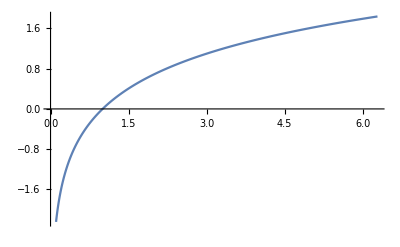

```mathematica
ListLinePlot[table]
```

```mathematica
M2TeXToString[M2TeXSetCommand["usepackage","Parameter"->{"asdf",asdf2,adsf,{asdf}}]]
```

\usepackage{asdf, asdf2, adsf, asdf}

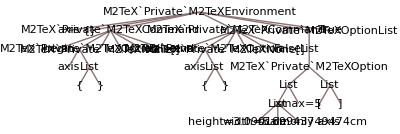

-Graphics-

```mathematica
M2TeXSetEnvironment[
"axis",
"ParameterList"->{
M2TeXSetOptionalOption[{
defaultM2TexPlotOptions,
"xmax=5"
}]
}
]//TreeForm
```

## PlotFunction

```mathematica
plotPDF[table_]:=Module[{},
M2TeXSetDocument["tikz"];
M2TeXAppendToDocument[M2TeXSetEnvironment["tikzpicture"]];
M2TeXAppendToDocument[M2TeXSetEnvironment[
"axis",
"ParameterList"->{
M2TeXSetOptionalOption[defaultM2TexPlotOptions]
}
]];
M2TeXAppendToDocument[M2TeXSetPlot[table,"black,thick"]];
M2TeXGeneratePdf["plot"]⟦1⟧
];
```

# MAtex stuff

```mathematica
(*True if file exists and is not a directory*)
fileQ[file_]:=FileType[file]===File
```

```mathematica
path=Quiet@Check[AbsoluteFileName@First@ReadList["!where pdflatex.exe",String,1],None]
```

```mathematica
dirpath=NotebookDirectory[]
```

```mathematica
$environment=Association@GetEnvironment[]
```

```mathematica
RunProcess[{path,"-halt-on-error","-interaction=nonstopmode","plot.tex"},ProcessDirectory->dirpath,ProcessEnvironment->$environment]
```

```mathematica
"\""
```

"

# new test

```mathematica
<<M2TeX`
```

```mathematica
test=M2TeXOption["option1","OpenCloseCharacter"->{"s","sdfsadf"}]
```

M2TeX`Private`M2TOption[<|Options→option1,OpenCloseCharacter→{s,sdfsadf}|>]

```mathematica
M2TeXToString[test]
```

soption1sdfsadf

```mathematica
test2=M2TeXOptionOptional[{"asdfadsf",{2}}]
%//M2TeXToString
```

M2TeX`Private`M2TOption[<|Options→{asdfadsf,{2}},OpenCloseCharacter→{[,]}|>]

[asdfadsf, 2]

```mathematica
M2TeXCommand["1a1"]
```

M2TeX`Private`M2TCommand[<|Name→1a1,Parameter→None,ParameterOptional→None,ParameterList→None,StartCharacter→\,EndCharacter→|>]

```mathematica
M2TeXCommand["1a1"]
%//M2TeXToString
```

M2TeX`Private`M2TCommand[<|Name→1a1,Parameter→None,ParameterOptional→None,ParameterList→None,StartCharacter→\,EndCharacter→|>]

\1a1

```mathematica
f["a"->1,"a"->2]
```

f[a→1,a→2]

```mathematica
M2TeXCommand["dsaf",5454,3]
%//M2TeXToString
```

M2TeX`Private`M2TCommand[<|Name→dsaf,Parameter→M2TeX`Private`M2TOption[<|Options→5454,OpenCloseCharacter→{{,}}|>],ParameterOptional→M2TeX`Private`M2TOption[<|Options→3,OpenCloseCharacter→{[,]}|>],ParameterList→None,StartCharacter→\,EndCharacter→|>]

\dsaf[3]{5454}

```mathematica
Table
```

# Demo Stuff

## Options

Full definition

```mathematica
M2TeXOption["value","OpenCloseCharacter"->{"<Open>","<Close>"}];
%//M2TeXToString
```

<Open>value<Close>

Default for options also works with list of options

```mathematica
M2TeXOption["value"];
%//M2TeXToString
M2TeXOption[{"value",{"op2",{"op3","op4"}}}];
%//M2TeXToString
```

{value}

{value, op2, op3, op4}

Optional options

```mathematica
M2TeXOptionOptional[{"optional1","optional2"}];
%//M2TeXToString
```

[optional1, optional2]

## Commands

Full definition

```mathematica
M2TeXCommand[
"dostuff",
"Parameter"->"val1",
"ParameterOptional"->"val2",
"ParameterList"->None,
"StartCharacter"->"<\\>",
"EndCharacter"->"</>"
];
%//M2TeXToString
```

<\>dostuff[val2]{val1}</>

With parameter list, the type of options can be given by the user

```mathematica
M2TeXCommand[
"dostuff",
"ParameterList"->{
M2TeXOption["op1"],
M2TeXOptionOptional[{"op2","op22"}],
M2TeXOption["op3"]
}
];
%//M2TeXToString
```

\dostuff{op1}[op2, op22]{op3}

Typical behavioud

```mathematica
M2TeXCommand["dostuff"];
%//M2TeXToString
M2TeXCommand["dostuff","opt"];
%//M2TeXToString
M2TeXCommand["dostuff","opt","opt2"];
%//M2TeXToString
M2TeXCommand["dostuff",,"opt2"];
%//M2TeXToString
```

\dostuff

\dostuff{opt}

\dostuff[opt2]{opt}

\dostuff[opt2]

Packages

```mathematica
M2TeXPackage["name",{"opt1","opt2"}];
%//M2TeXToString
```

\usepackage[opt1, opt2]{name}

## Environments

Full definition

```mathematica
M2TeXEnvironment["document","ParameterList"->{
M2TeXOption["op1"],
M2TeXOptionOptional["op2"]
}];
%//M2TeXToString
```

\begin{document}{op1}[op2]
\end{document}

Short definitions

```mathematica
M2TeXEnvironment["document"];
%//M2TeXToString
M2TeXEnvironment["document",{
M2TeXOption["op1"],
M2TeXOptionOptional["op2"]
}];
%//M2TeXToString
```

\begin{document}
\end{document}

\begin{document}{op1}[op2]
\end{document}